```mathematica
ClearAll["Global`*"]
```

```mathematica
Rexpr=x/(1-x);

coorsubs={u->ut,r->Rexpr}

Xcoor={u,r};

xcoor={ut,x};
```

{u→ut,r→x/(1-x)}

```mathematica
(Jac=Table[D[Xcoor[[c1]]/. coorsubs,xcoor[[c2]]],{c1,1,Length@Xcoor},{c2,1,Length@xcoor}])//MatrixForm
```

(1 | 0
0 | 1/(1-x)+x/(1-x)^2)

```mathematica
(InvJac=Inverse@Jac)//MatrixForm

Jac.InvJac
```

(1 | 0
0 | 1/(1/(1-x)+x/(1-x)^2))

{{1,0},{0,1}}

```mathematica
derchange=Table[D[zz_[u,r],Xcoor[[count]]]->Sum[InvJac[[sum,count]] D[zz[ut,x],xcoor[[sum]]],{sum,1,Length@xcoor}],{count,1,Length@Xcoor}]

changerules={derchange,zz_[u,r]->zz[ut,x]}//Flatten
```

{zz_^(1,0)[u,r]→zz^(1,0)[ut,x],zz_^(0,1)[u,r]→(zz^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2)}

{zz_^(1,0)[u,r]→zz^(1,0)[ut,x],zz_^(0,1)[u,r]→(zz^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2),zz_[u,r]→zz[ut,x]}

```mathematica
{Derivative[1,0][zz_][u,r]->Derivative[1,0][zz][ut,x],Derivative[0,1][zz_][u,r]->(Derivative[0,1][zz][ut,x])/(1/(1-x)+x/(1-x)^2),zz_[u,r]->zz[ut,x]}
```

{zz_^(1,0)[u,r]→zz^(1,0)[ut,x],zz_^(0,1)[u,r]→(zz^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2),zz_[u,r]→zz[ut,x]}

```mathematica
changerules
```

{zz_^(1,0)[u,r]→zz^(1,0)[ut,x],zz_^(0,1)[u,r]→(zz^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2),zz_[u,r]→zz[ut,x]}

## Wave equation in {u,x} coordinates, using m[u,x]

□  operator  (3.3.11)

```mathematica
Boxhψ [u,r]= Exp[-2β[u,r]]*(D[(V[u,r]/r),r]*D[ψ[u,r],r]-2*D[D[ψ[u,r],r],u]+V[u,r]/r*D[D[ψ[u,r],r],r])
```

ⅇ^(-2 β[u,r]) ((-V[u,r]/r^2+(V^(0,1)[u,r])/r) ψ^(0,1)[u,r]+(V[u,r] ψ^(0,2)[u,r])/r-2 ψ^(1,1)[u,r])

```mathematica
V[u,r]=Exp[2*β[u,r]]*(r-2*m[u,r])
```

ⅇ^(2 β[u,r]) (r-2 m[u,r])

```mathematica
Boxhψ[u,r]
```

ⅇ^(-2 β[u,r]) ((-(ⅇ^(2 β[u,r]) (r-2 m[u,r]))/r^2+(V^(0,1)[u,r])/r) ψ^(0,1)[u,r]+(ⅇ^(2 β[u,r]) (r-2 m[u,r]) ψ^(0,2)[u,r])/r-2 ψ^(1,1)[u,r])

```mathematica
(Boxhψ[u,r]-D[(V[u,r]/r),r]*Exp[-2*β[u,r]]*ψ[u,r]/r)/.changerules/.coorsubs/.V->Function[{u,r},(Exp[2*β[u,r]]*(r-2*m[u,r]))]
```

-(ⅇ^(-2 β[ut,x]) (1-x) ψ[ut,x] (-(ⅇ^(2 β[ut,x]) (1-x)^2 (x/(1-x)-2 m[ut,x]))/x^2+(ⅇ^(2 β[ut,x]) (1-x) (1-(2 m^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2)))/x+(2 ⅇ^(2 β[ut,x]) (1-x) (x/(1-x)-2 m[ut,x]) β^(0,1)[ut,x])/(x (1/(1-x)+x/(1-x)^2))))/x+ⅇ^(-2 β[ut,x]) (((-(ⅇ^(2 β[ut,x]) (1-x)^2 (x/(1-x)-2 m[ut,x]))/x^2+((1-x) (ⅇ^(2 β[ut,x]) (1-2 m^(0,1)[ut,x])+2 ⅇ^(2 β[ut,x]) (x-2 m[ut,x]) β^(0,1)[ut,x]))/(x (1/(1-x)+x/(1-x)^2))) ψ^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2)+(ⅇ^(2 β[ut,x]) (1-x) (x/(1-x)-2 m[ut,x]) ψ^(0,2)[ut,x])/x-2 ψ^(1,1)[ut,x])

```mathematica
Simplify[%]
```

(2 (-1+x)^3 ψ[ut,x] (x ((-1+x) m^(0,1)[ut,x]+x β^(0,1)[ut,x])+m[ut,x] (1+2 (-1+x) x β^(0,1)[ut,x])))/x^3+((1-x)^3 (-x-2 (-1+x) m[ut,x]+(-1+x)^2 x (1-2 m^(0,1)[ut,x]+2 (x-2 m[ut,x]) β^(0,1)[ut,x])) ψ^(0,1)[ut,x])/x^2+((x+2 (-1+x) m[ut,x]) ψ^(0,2)[ut,x])/x-2 ⅇ^(-2 β[ut,x]) ψ^(1,1)[ut,x]

```mathematica
Solve[%==0,D[D[ψ[ut,x],ut],x]]/.changerules/.coorsubs
```

{{ψ^(1,1)[ut,x]→-1/2 ⅇ^(2 β[ut,x]) (-(2 (-1+x)^3 ψ[ut,x] (x ((-1+x) m^(0,1)[ut,x]+x β^(0,1)[ut,x])+m[ut,x] (1+2 (-1+x) x β^(0,1)[ut,x])))/x^3-((1-x)^3 (-x-2 (-1+x) m[ut,x]+(-1+x)^2 x (1-2 m^(0,1)[ut,x]+2 (x-2 m[ut,x]) β^(0,1)[ut,x])) ψ^(0,1)[ut,x])/x^2-((x+2 (-1+x) m[ut,x]) ψ^(0,2)[ut,x])/x)}}

```mathematica
{{Derivative[1,1][ψ][ut,x]->-1/2 ⅇ^(2 β[ut,x]) (-(2 (-1+x)^3 ψ[ut,x] (x ((-1+x) Derivative[0,1][m][ut,x]+x Derivative[0,1][β][ut,x])+m[ut,x] (1+2 (-1+x) x Derivative[0,1][β][ut,x])))/x^3-(2 (-1+x)^4 (x ((-1+x) Derivative[0,1][m][ut,x]+x Derivative[0,1][β][ut,x])+m[ut,x] (1+2 (-1+x) x Derivative[0,1][β][ut,x])) Derivative[0,1][ψ][ut,x])/x^2-((x+2 (-1+x) m[ut,x]) Derivative[0,2][ψ][ut,x])/x)}}
```

{{ψ^(1,1)[ut,x]→-1/2 ⅇ^(2 β[ut,x]) (-(2 (-1+x)^3 ψ[ut,x] (x ((-1+x) m^(0,1)[ut,x]+x β^(0,1)[ut,x])+m[ut,x] (1+2 (-1+x) x β^(0,1)[ut,x])))/x^3-(2 (-1+x)^4 (x ((-1+x) m^(0,1)[ut,x]+x β^(0,1)[ut,x])+m[ut,x] (1+2 (-1+x) x β^(0,1)[ut,x])) ψ^(0,1)[ut,x])/x^2-((x+2 (-1+x) m[ut,x]) ψ^(0,2)[ut,x])/x)}}

```mathematica
-1/2 ⅇ^(2 β[ut,x]) (-(2 (-1+x)^3 ψ[ut,x] (x ((-1+x) Derivative[0,1][m][ut,x]+x Derivative[0,1][β][ut,x])+m[ut,x] (1+2 (-1+x) x Derivative[0,1][β][ut,x])))/x^3-(2 (-1+x)^4 (x ((-1+x) Derivative[0,1][m][ut,x]+x Derivative[0,1][β][ut,x])+m[ut,x] (1+2 (-1+x) x Derivative[0,1][β][ut,x])) Derivative[0,1][ψ][ut,x])/x^2-((x+2 (-1+x) m[ut,x]) Derivative[0,2][ψ][ut,x])/x)
```

```mathematica
`
```

expressão antiga:

```mathematica
-1/2 ⅇ^(2 β[ut,x]) (1/x^2 2 ⅇ^((2 (x-ψ+x ψ) β[ut,x])/x) (-1+x)^2 (x ((-1+x) Derivative[0,1][m][ut,x]+x Derivative[0,1][β][ut,x])+m[ut,x] (1+2 (-1+x) x Derivative[0,1][β][ut,x]))-((-1+x)^3 (x+2 (-1+x) m[ut,x]) Derivative[0,1][ψ][ut,x])/x^2-((1-x)^3 (1-2 (-1+x)^2 Derivative[0,1][m][ut,x]) Derivative[0,1][ψ][ut,x])/x-(2 (-1+x)^4 (x+2 (-1+x) m[ut,x]) Derivative[0,1][β][ut,x] Derivative[0,1][ψ][ut,x])/x-Derivative[0,2][ψ][ut,x]-(2 (-1+x) m[ut,x] Derivative[0,2][ψ][ut,x])/x)/.x->1
```

1/2 ⅇ^(2 β[ut,1]) ψ^(0,2)[ut,1]

This equation above is our 3rd evolution eq. found from the wave equation.

Let’s work on each of the three singular terms of (3.3.11) around r=0

```mathematica
m->Function[{u,r},1/6*r^3*m3[u]] (*because at the origin, dm/dm = O(r^2)*)
ψ->Function[{u,r},ψ1[u]*r] (*because ψ=a*r + O(r^2) and ψ->0 at the origin*)
```

m→Function[{u,r},1/6 r^3 m3[u]]

ψ→Function[{u,r},ψ1[u] r]

```mathematica
ψ->Function[{u,r},ψ1[u] r]
```

ψ→Function[{u,r},ψ1[u] r]

```mathematica
Series[D[V[u,r]/r,r]*Exp[-2*β[u,r]]*ψ[u,r]/r,{r,0,1}]/. Derivative[0,1][β][u,0]->0/.ψ->Function[{u,r},ψ1[u]*r]/.m->Function[{u,r},1/6*r^3*m3[u]]
```

-(ⅇ^(-2 β[u,0]) V[u,0] ψ1[u])/r^2+1/6 ⅇ^(-2 β[u,0]) (3 ψ1[u] V^(0,2)[u,0]+6 V[u,0] ψ1[u] β^(0,2)[u,0])-1/24 (ⅇ^(-2 β[u,0]) (-8 ψ1[u] V^(0,3)[u,0]-8 V[u,0] ψ1[u] β^(0,3)[u,0])) r+O[r]^2

which is 0 for r=0.

Next term:

```mathematica
Series[D[V[u,r]/r,r]*Exp[-2*β[u,r]]*D[ψ[u,r],r],{r,0,1}]/. Derivative[0,1][β][u,0]->0/.ψ->Function[{u,r},ψ1[u]*r]/.m->Function[{u,r},1/6*r^3*m3[u]]
```

-(ⅇ^(-2 β[u,0]) V[u,0] ψ1[u])/r^2+1/2 ⅇ^(-2 β[u,0]) (ψ1[u] V^(0,2)[u,0]+2 V[u,0] ψ1[u] β^(0,2)[u,0])+1/6 ⅇ^(-2 β[u,0]) (2 ψ1[u] V^(0,3)[u,0]+2 V[u,0] ψ1[u] β^(0,3)[u,0]) r+O[r]^2

which is 0 for r=0.

Next term:

```mathematica
Exp[2*β[u,r]]*(r-2*m[u,r])
```

```mathematica
V[u,r]=Exp[2*β[u,r]]*(r-2*m[u,r])
```

ⅇ^(2 β[u,r]) (r-2 m[u,r])

```mathematica
Series[Exp[-2*β[u,r]]*V[u,r]/r,{r,0,1}]/. Derivative[0,1][β][u,0]->0/.ψ->Function[{u,r},ψ1[u]*r]/.m->Function[{u,r},1/6*r^3*m3[u]]
```

1+O[r]^2

```mathematica
Series[Exp[-2*β[u,r]]*V[u,r]/r*D[D[ψ[u,r],r],r],{r,0,1}]/. Derivative[0,1][β][u,0]->0/.ψ->Function[{u,r},ψ1[u]*r]/.m->Function[{u,r},1/6*r^3*m3[u]]
```

O[r]^2

^Only non zero term!

All three formally singular terms of (3.3.11) are 0 around r=0. The wave equation then yields

```mathematica
eq1=-2*Exp[-2*β[u,r]]*D[D[ψ[u,r],r],u]==0
eq1/.changerules/.coorsubs
```

-2 ⅇ^(-2 β[u,r]) ψ^(1,1)[u,r]==0

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {coorsubs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2 ⅇ^(-2 β[u,r]) ψ^(1,1)[u,r]==0/.changerules/.coorsubs

```mathematica
Solve[eq1,D[D[ψ[ut,x],ut],x]]
```

{}

## EFE equations

Computing (dϕ/dx)^2

```mathematica
Clear[ϕ]
ϕ[u,x]=ψ[u,x]*(1-x)/x
```

((1-x) ψ[u,x])/x

```mathematica
D[ϕ[u,x],x]
```

-((1-x) ψ[u,x])/x^2-ψ[u,x]/x+((1-x) ψ^(0,1)[u,x])/x

```mathematica
Simplify[%]
```

-(ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])/x^2

β equation

```mathematica
(-(ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])/x^2)^2*2π*x*(1-x)
```

(2 π (1-x) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Simplify[%]
```

-(2 π (-1+x) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Eq2=D[β[u,x],x]==%
```

β^(0,1)[u,x]==-(2 π (-1+x) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Derivative[0,1][β][u,x]==-(2 π (-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3
```

```mathematica
Series[(ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2,{x,0,2}]
```

ψ[u,0]^2+ψ[u,0] (2 ψ^(0,1)[u,0]-ψ^(0,2)[u,0]) x^2+O[x]^3

```mathematica
Series[(ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2,{x,0,3}]/.ψ[u,0]->0
```

O[x]^4

```mathematica
Series[(-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2,{x,0,4}]/.ψ[u,0]->0
```

-(ψ^(0,1)[u,0]-1/2 ψ^(0,2)[u,0])^2 x^4+O[x]^5

so the numerator goes to 0 faster than the denominator. D[beta,x]->0 at the origin

right boundary condition

```mathematica
-(2 π (-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/.x->1
```

0

```mathematica
jacobian[x_]=2x(sech(x^2/(1-x^2)))^2/(1-x^2)^2
```

(2 sech^2 x^5)/((1-x^2)^4)

```mathematica
jacobian[x]/.x->1
```

Power::infy: Infinite expression 1/0^(3/2) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Indeterminate

```mathematica
(-(2 π (-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/jacobian[x])/.x->1
```

Power::infy: Infinite expression 1/(√0) encountered.

Indeterminate

m equation

```mathematica
(-(ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])/x^2)^2*2*π*x^2*(1-2*(1-x)*m[u,x]/x)
```

(2 π (1-(2 (1-x) m[u,x])/x) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^2

```mathematica
Simplify[%]
```

(2 π (x+2 (-1+x) m[u,x]) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Eq3=D[m[u,x],x]==%
```

m^(0,1)[u,x]==(2 π (x+2 (-1+x) m[u,x]) (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Series[2 π (x+2 (-1+x) m[u,x]) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2,{x,0,3}]/.ψ[u,0]->0
```

O[x]^4

right boundary condition

```mathematica
(2 π (x+2 (-1+x) m[u,x]) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/.x->1
```

2 π ψ[u,1]^2

## Changing gridpoints

```mathematica
Series[-1/2 * (1-x)^2*Exp[2*β[u,r]]*(1-2  m[u,x]*(1-x)/x) ,{x,0,3}]/.ψ[u,0]->0/. Derivative[0,1][β][u,0]->0/.ψ->Function[{u,r},ψ1[u]*r]/.m->Function[{u,r},1/6*r^3*m3[u]]
```

-1/2 ⅇ^(2 β[u,r])+ⅇ^(2 β[u,r]) x-1/6 (ⅇ^(2 β[u,r]) (3-m3[u])) x^2-1/2 (ⅇ^(2 β[u,r]) m3[u]) x^3+O[x]^4

## Initial data

```mathematica
D[(x/(1-x))^3*e^(-((x/(1-x)-r0)/σ)^2),x]
```

(3 e^(-(-r0+x/(1-x))^2/σ^2) x^2)/(1-x)^3+(3 e^(-(-r0+x/(1-x))^2/σ^2) x^3)/(1-x)^4-(2 e^(-(-r0+x/(1-x))^2/σ^2) x^3 (1/(1-x)+x/(1-x)^2) (-r0+x/(1-x)) Log[e])/((1-x)^3 σ^2)

```mathematica
Simplify[(3 e^(-(-r0+x/(1-x))^2/σ^2) x^2)/(1-x)^3+(3 e^(-(-r0+x/(1-x))^2/σ^2) x^3)/(1-x)^4-(2 e^(-(-r0+x/(1-x))^2/σ^2) x^3 (1/(1-x)+x/(1-x)^2) (-r0+x/(1-x)) Log[e])/((1-x)^3 σ^2)]
```

(e^(-(r0 (-1+x)+x)^2/((-1+x)^2 σ^2)) x^2 (3 (-1+x)^2 σ^2-2 x (r0 (-1+x)+x) Log[e]))/((-1+x)^6 σ^2)

## New coordinate system with more resolution for small x (june 2023)

```mathematica
coord_change[x]=Tanh[(x/4)/(Sqrt[1-x^2])]
```

Tanh[x/(4 √(1-x^2))]

```mathematica
jacobian[x]=(Sech[x/(4.0*(Sqrt[1-x^2]))])^2/((1-x^2)*4*(Sqrt[1-x^2]))
```

(Sech[(0.25 x)/(√(1-x^2))]^2)/(4 (1-x^2)^(3/2))

```mathematica
Series[(-(2 π (-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/jacobian[x]),{x,1,3}]
```

Cosh[(0.176777 √(-1+x))/(√(1-x) √(x-1))+(0.132583 √(-1+x) √(x-1))/(√(1-x))-(0.0276214 √(-1+x) (x-1)^(3/2))/(√(1-x))+(0.00966748 √(-1+x) (x-1)^(5/2))/(√(1-x))+O[x-1]^(7/2)]^2 (-(16 (√2 π (1-x)^(3/2) ψ[u,1]^2) (x-1)^(5/2))/(-1+x)^(3/2)+O[x-1]^(7/2))

```mathematica
Simplify[%]
```

Cosh[(0.176777 √(-1+x))/(√(1-x) √(x-1))+(0.132583 √(-1+x) √(x-1))/(√(1-x))-(0.0276214 √(-1+x) (x-1)^(3/2))/(√(1-x))+(0.00966748 √(-1+x) (x-1)^(5/2))/(√(1-x))+O[x-1]^(7/2)]^2 ((16 √2 π √(1-x) ψ[u,1]^2 (x-1)^(5/2))/(√(-1+x))+O[x-1]^(7/2))

```mathematica
Limit[(-(2 π (-1+x) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/jacobian[x]),x->1]
```

lim_(x→1) -(8 π (-1+x) (1-x^2)^(3/2) Cosh[(0.25 x)/(√(1-x^2))]^2 (ψ[u,x]+(-1+x) x ψ^(0,1)[u,x])^2)/x^3

```mathematica
Series[(-1+x) (1-x^2)^(3/2) Cosh[(0.25 x)/(√(1-x^2))]^2,{x,1,1}]
```

Cosh[(0.176777 √(-1+x))/(√(1-x) √(x-1))+(0.132583 √(-1+x) √(x-1))/(√(1-x))+O[x-1]^(3/2)]^2 O[x-1]^(5/2)

```mathematica
Simplify[%]
```

Cosh[(0.176777 √(-1+x))/(√(1-x) √(x-1))+(0.132583 √(-1+x) √(x-1))/(√(1-x))-(0.0276214 √(-1+x) (x-1)^(3/2))/(√(1-x))+(0.00966748 √(-1+x) (x-1)^(5/2))/(√(1-x))+O[x-1]^(7/2)]^2 ((2 √2 (1-x)^(3/2) (x-1)^(5/2))/(-1+x)^(3/2)+O[x-1]^(7/2))

```mathematica
f[x_]=Tanh[x/4/Sqrt[1-x^2]]
```

Tanh[x/(4 √(1-x^2))]

```mathematica
D[f[x],x]
```

(x^2/(4 (1-x^2)^(3/2))+1/(4 √(1-x^2))) Sech[x/(4 √(1-x^2))]^2

```mathematica
Simplify[(x^2/(4 (1-x^2)^(3/2))+1/(4 √(1-x^2))) Sech[x/(4 √(1-x^2))]^2]
```

(Sech[x/(4 √(1-x^2))]^2)/(4 (1-x^2)^(3/2))

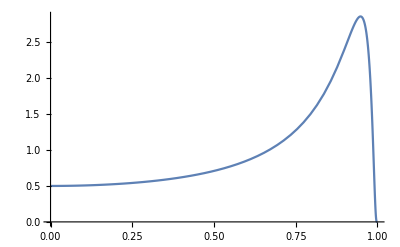

```mathematica
Plot[(Sech[x/(2 √(1-x^2))]^2)/(2 (1-x^2)^(3/2)),{x,0,1}]
```

```mathematica
g[x_]=Tanh[x^2/(1-x^2)]
```

```mathematica
D[g[x],x]
```

((2 x^3)/((1-x^2)^2)+(2 x)/(1-x^2)) Sech[x^2/(1-x^2)]^2

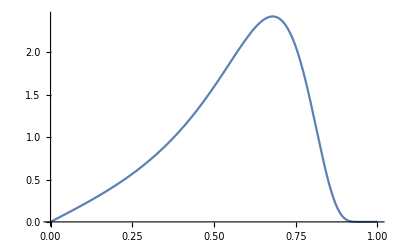

```mathematica
Plot[((2 x^3)/((1-x^2)^2)+(2 x)/(1-x^2)) Sech[x^2/(1-x^2)]^2,{x,0,1}]
```

```mathematica
n=100
dx=1/n
```

100

1/100

```mathematica
h[x_]=(1/2+1/2*Cos[(2*x/dx-1)*Pi/(2*n)])
```

1/2+1/2 Cos[1/200 π (-1+200 x)]

new chebyshev s.t. j[0]=0

```mathematica
j[x_]=1/2+1/2 Cos[Pi(1-x)]
```

1/2+1/2 Cos[π (1-x)]

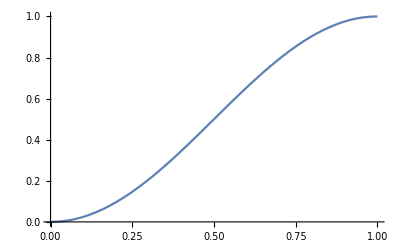

```mathematica
Plot[%,{x,0,1}]
```

```mathematica
D[j[x],x]
```

1/4 π Sin[1/2 π (1-x)]

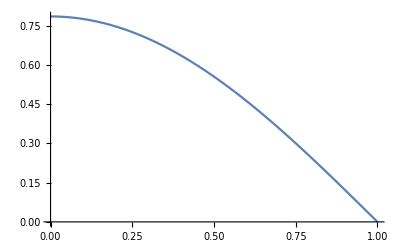

```mathematica
Plot[%,{x,0,1}]
```

```mathematica
D[h[x],x]
```

h'[x]

```mathematica
Plot[%,{x,0,1}]
```

-Graphics-

```mathematica
Series[D[j[x],x],{x,1,4}]
```

-1/2 π^2 (x-1)+1/12 π^4 (x-1)^3+O[x-1]^5

```mathematica
(2 π (x+2 (-1+x) m[u,x]) (ψ[u,x]+(-1+x) x Derivative[0,1][ψ][u,x])^2)/x^3/.x->1
```

2 π ψ[u,1]^2

```mathematica
D[Sin[u+r],r]/.changerules
Cos[r+u]
Clear[f]
D[f[u,r],r]/.changerules
(Derivative[0,1][f][ut,x])/(1/(1-x)+x/(1-x)^2)
f[u,r]:=Sin[u+r]*Sin[u+r]
D[f[u,r],r]/.changerules
2 Cos[r+u] Sin[r+u]
(2 Cos[r+u] Sin[r+u])/.changerules
2 Cos[r+u] Sin[r+u]
D[f[u,r],{r,2}]/.coorsubs
2 Cos[ut+x/(1-x)]^2-2 Sin[ut+x/(1-x)]^2
Clear[f]
Clear[u]
Clear[r]
Clear[x]
D[f[u,r[x]],{x,2}]
r''[x] Derivative[0,1][f][u,r[x]]+r'[x]^2 Derivative[0,2][f][u,r[x]]
Clear[f]
Clear[u]
Clear[r]
Clear[x]
D[f[u,x[r]],{r,2}]
x''[r] Derivative[0,1][f][u,x[r]]+x'[r]^2 Derivative[0,2][f][u,x[r]]
Clear[f]
Clear[u]
Clear[r]
Clear[x]
D[f[u,x[r]],r]
x'[r] Derivative[0,1][f][u,x[r]]
D[1/(1+x)^2,x]
-2/(1+x)^3

Clear[f]
A[u,r]=1/r*D[f[u,r],r]
A[u,r]/.changerules
(Derivative[0,1][f][u,r])/r
(Derivative[0,1][f][ut,x])/(r (1/(1-x)+x/(1-x)^2))
```

Limit::lim: Limit specification 0 is not of the form x -> x0.

Limit[x^2,0]

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Cos[r+u]/.changerules

Cos[r+u]

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

f^(0,1)[u,r]/.changerules

(f^(0,1)[ut,x])/(1/(1-x)+x/(1-x)^2)

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 Cos[r+u] Sin[r+u]/.changerules

2 Cos[r+u] Sin[r+u]

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 Cos[r+u] Sin[r+u]/.changerules

2 Cos[r+u] Sin[r+u]

ReplaceAll::reps: {coorsubs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2 Cos[r+u]^2-2 Sin[r+u]^2/.coorsubs

2 Cos[ut+x/(1-x)]^2-2 Sin[ut+x/(1-x)]^2

r''[x] f^(0,1)[u,r[x]]+r'[x]^2 f^(0,2)[u,r[x]]

r''[x] f^(0,1)[u,r[x]]+r'[x]^2 f^(0,2)[u,r[x]]

x''[r] f^(0,1)[u,x[r]]+x'[r]^2 f^(0,2)[u,x[r]]

x''[r] f^(0,1)[u,x[r]]+x'[r]^2 f^(0,2)[u,x[r]]

x'[r] f^(0,1)[u,x[r]]

x'[r] f^(0,1)[u,x[r]]

-2/(1+x)^3

-2/(1+x)^3

(f^(0,1)[u,r])/r

ReplaceAll::reps: {changerules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(f^(0,1)[u,r])/r/.changerules

(f^(0,1)[u,r])/r

(f^(0,1)[ut,x])/(r (1/(1-x)+x/(1-x)^2))